```mathematica
SetDirectory[NotebookDirectory[]]
dx=0.1;
dy=0.1;
buf=0;
xmax=16;
ymax=16;
xcm= Round[(2 xmax)/dx  +buf ]
ycm=Round[(2 ymax)/dy  +buf] 
FILESIZE = ( xcm*ycm)*8
FileByteCount["init/t00.bin"]



τ0 = 0.2;
trace[mat_]:= mat[[1,1]]-mat[[2,2]]-mat[[3,3]]- τ0^2 mat[[4,4]]
dataXY[mat_]:={Table[{-xmax+(i-1)dx ,-ymax+(j-1) dy ,mat[[i,j]]},{i,1,xcm},{j,1,ycm}]};

axesXY[text_] := {AxesLabel->{"X (in fm)","Y (in fm)"},PlotLabel->text,LabelStyle->{Black,Bold},PlotStyle->{{White,Thick},{Red,Thick}},PlotRange->All};


GEVFM=0.1973;
E1 =(0.5028563305441270) ;
E2 =(1.62) ;
E3 =(1.86) ;
E4 =(9.9878355786273545)  ;
s95pP =Compile[{{en,_Real}},
Module[{ret,enfm},
enfm=en;
enfm *= GEVFM;
ret = Piecewise[{
{(0.3299*(E^(0.4346*enfm)-1)),enfm≤ E1},
{( 1.024 10^-7*E^(6.041*enfm)+0.007273+0.14578 enfm ),enfm>E1 && enfm≤E2},
{( 0.30195  E^(0.31308 enfm)-0.256232 ),enfm>E2&& enfm≤E3},
{(  0.332 enfm -0.3223 enfm^0.4585  +0.1167 enfm^-1.233 -0.003906 enfm E^(-0.05697 enfm) +0.1436 enfm E^(-0.9131*en) ),enfm>E3&& enfm≤E4},
{  ( 0.3327 enfm -0.3223 enfm^0.4585-0.003906 enfm E^(-0.05697 enfm)  ) ,enfm>E4}
}
];
ret/GEVFM
]
]
(*EIGEN VALUE SEARCH*)
entab=Table[0,{i,1,xcm},{j,1,ycm}];
vxtab=Table[0,{i,1,xcm},{j,1,ycm}];
vytab=Table[0,{i,1,xcm},{j,1,ycm}];
vztab=Table[0,{i,1,xcm},{j,1,ycm}];
p1tab=Table[0,{i,1,xcm},{j,1,ycm}];
p2tab=Table[0,{i,1,xcm},{j,1,ycm}];
p3tab=Table[0,{i,1,xcm},{j,1,ycm}];
p4tab=Table[0,{i,1,xcm},{j,1,ycm}];
p5tab=Table[0,{i,1,xcm},{j,1,ycm}]; 
Tμνtab=Table[0,{l,1,4},{m,1,4},{i,1,xcm},{j,1,ycm} ]; 
TμνIdealtab=Table[0,{l,1,4},{m,1,4},{i,1,xcm},{j,1,ycm} ]; 
Wμνtab=Table[0,{l,1,4},{m,1,4},{i,1,xcm},{j,1,ycm} ]; 
πμνtab=Table[0,{l,1,4},{m,1,4},{i,1,xcm},{j,1,ycm} ]; 
Πtab=Table[0,{l,1,4},{m,1,4},{i,1,xcm},{j,1,ycm} ];
```

C:\Users\sidux\Desktop\NEWEST10

320

320

819200

819200

CompiledFunction[…]

```mathematica
a= 5.5 10^-7;
s95pP[a]
s95pP[a]/a
0.1434 a
```

7.8856×10^-8

0.143375

7.887×10^-8

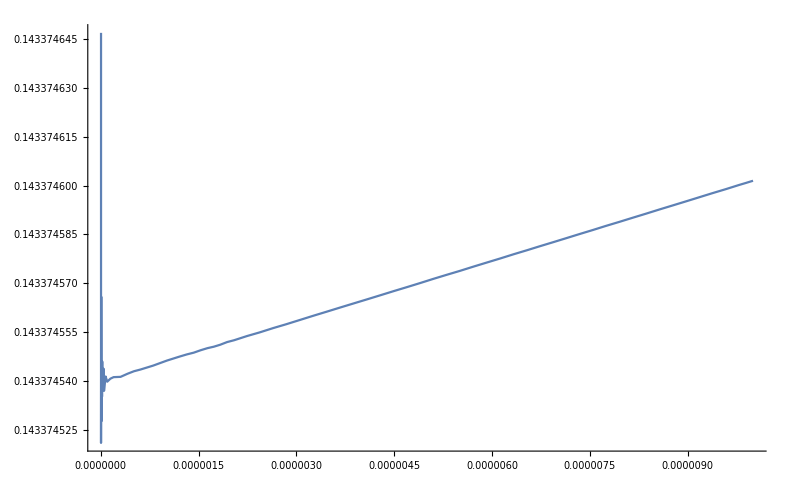

```mathematica
Plot[s95pP[a]/a,{a,0.5 10^-14,10^-5}]
```

```mathematica
Istmpe1=OpenRead["init/t00.bin",BinaryFormat->True] 
Istmpe2=OpenRead["init/t01.bin",BinaryFormat->True] ;
Istmpe3=OpenRead["init/t02.bin",BinaryFormat->True] ;
Istmpe4=OpenRead["init/t03.bin",BinaryFormat->True]  ;
Istmpe5=OpenRead["init/t11.bin",BinaryFormat->True]  ;
Istmpe6=OpenRead["init/t12.bin",BinaryFormat->True] ;
Istmpe7=OpenRead["init/t13.bin",BinaryFormat->True] ;
Istmpe8=OpenRead["init/t22.bin",BinaryFormat->True] ;
Istmpe9=OpenRead["init/t23.bin",BinaryFormat->True] ;
Istmpe10=OpenRead["init/t33.bin",BinaryFormat->True] ;
 
For[i=1,i<=xcm,i++,
For[j=1,j<=ycm,j++,
Tμνtab[[1,1,i,j]]=BinaryRead[Istmpe1,"Real64"];
Tμνtab[[1,2,i,j]]=BinaryRead[Istmpe2,"Real64"];
Tμνtab[[2,1,i,j]]=Tμνtab[[1,2,i,j]];
Tμνtab[[1,3,i,j]]=BinaryRead[Istmpe3,"Real64"];
Tμνtab[[3,1,i,j]]=Tμνtab[[1,3,i,j]];
Tμνtab[[1,4,i,j]]=BinaryRead[Istmpe4,"Real64"];
Tμνtab[[4,1,i,j]]=Tμνtab[[1,4,i,j]];
Tμνtab[[2,2,i,j]]=BinaryRead[Istmpe5,"Real64"]; 
Tμνtab[[2,3,i,j]]=BinaryRead[Istmpe6,"Real64"];
Tμνtab[[3,2,i,j]]=Tμνtab[[2,3,i,j]]  ;
Tμνtab[[2,4,i,j]]=BinaryRead[Istmpe7,"Real64"];
Tμνtab[[4,2,i,j]]=Tμνtab[[2,4,i,j]]  ; 
Tμνtab[[3,3,i,j]]=BinaryRead[Istmpe8,"Real64"];
Tμνtab[[3,4,i,j]]=BinaryRead[Istmpe9,"Real64"];
Tμνtab[[4,3,i,j]]=Tμνtab[[3,4,i,j]];
Tμνtab[[4,4,i,j]]=BinaryRead[Istmpe10,"Real64"];
]
]

 Close[Istmpe1];
 Close[Istmpe2];
 Close[Istmpe3];
 Close[Istmpe4];
 Close[Istmpe5];
 Close[Istmpe6];
 Close[Istmpe7];
 Close[Istmpe8];
 Close[Istmpe9]; Close[Istmpe10]
```

InputStream[…]

init/t33.bin

```mathematica
MatrixForm[Tμνtab[[All,All,161,161]]]
trace[Tμνtab[[All,All,161,161]]]
```

```mathematica
guu = {{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1/τ0^2}};
gdd={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-τ0^2}};
gud=  {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}; 
For[i=1,i<=xcm,i++,
For[j=1,j<=ycm,j++, 
TμνField= Tμνtab[[All,All,i,j]];
X=-xmax+(i-1)*dx;
Y=-ymax+(j-1)*dy;
{vals,vecs}=Eigensystem[TμνField.gdd];
ikey=0;
index=-1;
Do[
If[
vecs[[  m,1 ]]==0,
Continue[];
,
vecs[[m]] = {1,vecs[[m,2]]/vecs[[m,1]], vecs[[m,3]]/vecs[[m,1]] ,vecs[[m,4]]/vecs[[m,1]]};
If[
Im[vecs[[  m,2 ]]  ]==0
&&Im[vecs[[  m,3]] ]==0
&&Im[vecs[[  m,4]] ]==0
&&Abs[vecs[[  m,2 ]] ]<1
&&Abs[vecs[[  m,3 ]] ]<1
&&Abs[vecs[[  m,4 ]] ]<1
&&Norm[{vecs[[  m,2 ]],vecs[[  m,3 ]],vecs[[  m,4 ]]}]<1
,
ikey++;
index=m;
];
];
,{m,1,4}];


If[ikey==1,
En=vals[[index]];
Vx=vecs[[index,2]];
Vy=vecs[[index,3]];
Vz=vecs[[index,4]];
,
Print[X];
Print[i];
Print[Y];
Print[j];
Print[vals];
Print[vecs[[1]]];
Print[vecs[[2]]];
Print[vecs[[3]]];
Print[vecs[[4]]];
Abort[]
];
 
G=1/(√(1-Vx^2-Vy^2-τ0^2 Vz^2));

u0=G;
u1=u0 Vx;
u2=u0 Vy;
u3=u0 Vz;
P=s95pP[En];
uupμ = {u0 ,u1 , u2 ,u3  };
udoμ= {u0 ,-u1 , -u2 ,-τ0^2 u3 };
dud = gud -Outer[Times,uupμ,udoμ] ;
duu = guu-Outer[Times,uupμ,uupμ];
TμνIdeal=((En+P ) Outer[Times, uupμ,uupμ] - P  guu );
TμνIdealtab[[All,All,i,j]] = TμνIdeal ; 
Wμ=dud.(udoμ.TμνField);
Wμν= Outer[Times, Wμ,uupμ]+Outer[Times, uupμ,Wμ];
Wμνtab[[All,All,i,j]] = Wμν;

PI = (trace[TμνField]-trace[TμνIdeal]-trace[Wμν])/3;

PIμν= PI duu;
Πtab[[All,All,i,j]]=PIμν ;

πμνtab[[All,All,i,j]] =  TμνField- TμνIdeal-Wμν-PIμν;

entab[[i,j]]=En;
vxtab[[i,j]]=Vx;
vytab[[i,j]]=Vy;
vztab[[i,j]]=Vz;
 
]
]
```

```mathematica
X=0;
Y=0;
i=IntegerPart[(X+xmax)/dx +1]
j=IntegerPart[(Y+ymax)/dy +1]

MatrixForm[Tμνtab[[All,All,i,j]]]
MatrixForm[TμνIdealtab[[All,All,i,j]]]
MatrixForm[Wμνtab[[All,All,i,j]]]
MatrixForm[Πtab[[All,All,i,j]]]
MatrixForm[πμνtab[[All,All,i,j]]]

Print["******  TRACES ********"]

trace[Tμνtab[[All,All,i,j]]]
trace[TμνIdealtab[[All,All,i,j]]]
trace[Wμνtab[[All,All,i,j]]]
trace[Πtab[[All,All,i,j]]]
trace[πμνtab[[All,All,i,j]]]
(*

ListPlot3D[Wμνtab[[1,1]]]*)
```

161

161

(524.212 | 0. | 0. | -1.84741×10^-13
0. | -1.55778 | 0. | 80.4333
0. | 0. | -1.55778 | 0.
-1.84741×10^-13 | 80.4333 | 0. | 13183.2)

(524.212 | 0. | 0. | 0.
0. | 160.696 | 0. | 0.
0. | 0. | 160.696 | 0.
0. | 0. | 0. | 4017.4)

(0. | 0. | 0. | -1.84741×10^-13
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
-1.84741×10^-13 | 0. | 0. | 0.)

(0. | 0. | 0. | 0.
0. | 14.0415 | 0. | 0.
0. | 0. | 14.0415 | 0.
0. | 0. | 0. | 351.038)

(0. | 0. | 0. | 0.
0. | -176.295 | 0. | 80.4333
0. | 0. | -176.295 | 0.
0. | 80.4333 | 0. | 8814.76)

******  TRACES ********

-1.13687×10^-13

42.1246

0.

-42.1246

5.68434×10^-14

```mathematica
ListPlot3D[dataXY[entab],axesXY["en"]]
ListPlot3D[dataXY[vxtab],axesXY["vx"]]
ListPlot3D[dataXY[vytab],axesXY["vy"]]
ListPlot3D[dataXY[vztab],axesXY["vz"]]
ListPlot3D[dataXY[p1tab],axesXY["p11"]]
ListPlot3D[dataXY[p2tab],axesXY["p22"]]
ListPlot3D[dataXY[p3tab],axesXY["p12"]]
ListPlot3D[dataXY[p4tab],axesXY["p13"]]
ListPlot3D[dataXY[p5tab],axesXY["p23"]]
```